```mathematica
(*css zebrafinch model*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
(*leave Q in matrix different than one up above recursions*)
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO Q), vh((1-lhO) vI z +lhO Q ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- Q) ), vh((1-lhO) vI (1-z)+lhO(1- Q) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa];
```

```mathematica
subs = {ba->3,bn->1,z->.8,vs->.6,vh->.9,vI->.7  ,u->.2, pa -> 0.1, pn-> 0.9}
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
```

{ba→3,bn→1,z→0.8,vs→0.6,vh→0.9,vI→0.7,u→0.2,pa→0.1,pn→0.9}

```mathematica
Fasols[[1,1,2]]/.subs/.test (*check it is stable qhat with values, select positive q-hat*)
 Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
 Fasols/.subs/.test
```

0.534226

{{Fa→0.534226},{Fa→-1.29983}}

```mathematica
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
```

```mathematica
AA
AA2=AA/.{Q->Qh}/.subs
```

{{0,0,ba pa,bn pn},{0,0,ba (1-pa),bn (1-pn)},{vs (lsO Q+(1-lsO) vI z),vh (lhO Q+(1-lhO) vI z),0,0},{vs (lsO (1-Q)+(1-lsO) vI (1-z)),vh (lhO (1-Q)+(1-lhO) vI (1-z)),0,0}}

{{0,0,0.3,0.9},{0,0,2.7,0.1},{0.6 (0.56 (1-lsO)+lsO Qh),0.9 (0.56 (1-lhO)+lhO Qh),0,0},{0.6 (0.14 (1-lsO)+lsO (1-Qh)),0.9 (0.14 (1-lhO)+lhO (1-Qh)),0,0}}

```mathematica
LL=Eigenvalues[AA2];
```

```mathematica
Eigenvalues[AA2]/.subs/.test /.Qh-> 0.5
```

{-1.26315,1.26315,0.-0.369405 ⅈ,0.+0.369405 ⅈ}

```mathematica
(*should i substitute Qhat for home condition in before eigenvalues?, also see if i can find positive one automatically*)
```

```mathematica
(*isolate Dominant eigenvalue, substitute in q-hat*)
Lambda1= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO] ];
```

```mathematica
softmaxsubs ={lsO -> Exp[llsO]/(1 +  Exp[llsO]) , lhO -> Exp[llhO]/(1 +  Exp[llhO]) ,LSO -> Exp[LLSO]/(1 +  Exp[LLSO]) , LHO -> Exp[LLHO]/(1 +  Exp[LLHO]) };
```

```mathematica
Lambda2[ llsO_, llhO_,LLHO_,LLSO_]:=Lambda1 /.softmaxsubs;
```

```mathematica
(*take partial derivatives then substitute mutant for common type//check if order of operations is right*)
DllsO=D[Lambda2[llsO, llhO,LLHO,LLSO],llsO]/. {LLHO -> llhO,LLSO-> llsO};
```

```mathematica
DllhO=D[Lambda2[llsO, llhO,LLHO,LLSO],llhO]/. {LLHO -> llhO,LLSO-> llsO};
```

```mathematica
(*try and graph*)
(*-4 is around 1% on logg-odds scale*)
llsOstart=-4;
llhOstart=4 ;
imax=1000;
llsItab=Table[0,{i,imax}];
llhItab=Table[0,{i,imax}];
llsOtab=Table[0,{i,imax}];
llhOtab=Table[0,{i,imax}];
DllsOtab=Table[0,{i,imax}];
DllhOtab=Table[0,{i,imax}];
delta=6;
llsOtab[[1]]=llsOstart;
llhOtab[[1]]=llhOstart;

DllsOtab[[1]]=DllsO/.subs/.{llsO->llsOstart,llhO->llhOstart}
DllhOtab[[1]]=DllhO/.subs/.{llsO->llsOstart,llhO->llhOstart}
```

-0.0000598998

-0.000212392

```mathematica
For[i=2,i<imax,i++,{

llsOtab[[i]]=llsOtab[[i-1]]  + delta DllsO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};
llhOtab[[i]]=llhOtab[[i-1]]  + delta DllhO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};

DllsOtab[[i]]=DllsO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};
DllhOtab[[i]]=DllhO/.subs/.{llsO->llsOtab[[i-1]],llhO->llhOtab[[i-1]]};
}];
```

```mathematica
lsOtab =Exp[llsOtab]/(1+Exp[llsOtab]);
lhOtab =Exp[llhOtab]/(1+Exp[llhOtab]);
```

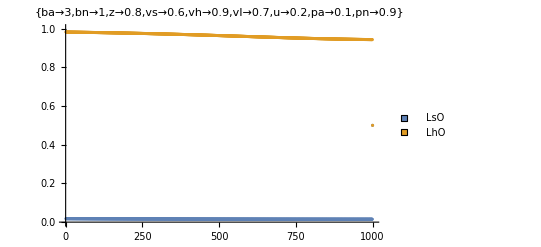

```mathematica
ListPlot[{lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsO,LhO},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->subs]
```

```mathematica
lsOtab
```

{1/((1+1/ⅇ^4) ⅇ^4),0.0179799,0.0179735,0.0179672,0.0179609,0.0179546,0.0179482,0.017942,0.0179357,0.0179294,0.0179231,0.0179168,0.0179106,0.0179043,0.0178981,0.0178919,0.0178856,0.0178794,0.0178732,0.017867,0.0178608,0.0178546,0.0178484,0.0178423,0.0178361,0.0178299,0.0178238,0.0178177,0.0178115,0.0178054,0.0177993,0.0177932,0.0177871,0.017781,0.0177749,0.0177688,0.0177628,0.0177567,0.0177507,0.0177446,0.0177386,0.0177326,0.0177265,0.0177205,0.0177145,0.0177085,0.0177025,0.0176965,0.0176906,0.0176846,0.0176787,0.0176727,0.0176668,0.0176608,0.0176549,0.017649,0.0176431,0.0176372,0.0176313,0.0176254,0.0176195,0.0176136,0.0176078,0.0176019,0.0175961,0.0175902,0.0175844,0.0175786,0.0175727,0.0175669,0.0175611,0.0175553,0.0175495,0.0175438,0.017538,0.0175322,0.0175265,0.0175207,0.017515,0.0175092,0.0175035,0.0174978,0.0174921,0.0174864,0.0174807,0.017475,0.0174693,0.0174637,0.017458,0.0174523,0.0174467,0.017441,0.0174354,0.0174298,0.0174242,0.0174186,0.0174129,0.0174074,0.0174018,0.0173962,0.0173906,0.017385,0.0173795,0.0173739,0.0173684,0.0173629,0.0173573,0.0173518,0.0173463,0.0173408,0.0173353,0.0173298,0.0173243,0.0173188,0.0173134,0.0173079,0.0173025,0.017297,0.0172916,0.0172861,0.0172807,0.0172753,0.0172699,0.0172645,0.0172591,0.0172537,0.0172483,0.017243,0.0172376,0.0172322,0.0172269,0.0172216,0.0172162,0.0172109,0.0172056,0.0172003,0.017195,0.0171897,0.0171844,0.0171791,0.0171738,0.0171685,0.0171633,0.017158,0.0171528,0.0171476,0.0171423,0.0171371,0.0171319,0.0171267,0.0171215,0.0171163,0.0171111,0.0171059,0.0171008,0.0170956,0.0170904,0.0170853,0.0170801,0.017075,0.0170699,0.0170648,0.0170597,0.0170545,0.0170494,0.0170444,0.0170393,0.0170342,0.0170291,0.0170241,0.017019,0.017014,0.0170089,0.0170039,0.0169989,0.0169939,0.0169889,0.0169838,0.0169789,0.0169739,0.0169689,0.0169639,0.0169589,0.016954,0.016949,0.0169441,0.0169392,0.0169342,0.0169293,0.0169244,0.0169195,0.0169146,0.0169097,0.0169048,0.0168999,0.0168951,0.0168902,0.0168853,0.0168805,0.0168756,0.0168708,0.016866,0.0168612,0.0168563,0.0168515,0.0168467,0.0168419,0.0168372,0.0168324,0.0168276,0.0168228,0.0168181,0.0168133,0.0168086,0.0168039,0.0167991,0.0167944,0.0167897,0.016785,0.0167803,0.0167756,0.0167709,0.0167663,0.0167616,0.0167569,0.0167523,0.0167476,0.016743,0.0167383,0.0167337,0.0167291,0.0167245,0.0167199,0.0167153,0.0167107,0.0167061,0.0167015,0.016697,0.0166924,0.0166878,0.0166833,0.0166788,0.0166742,0.0166697,0.0166652,0.0166607,0.0166562,0.0166517,0.0166472,0.0166427,0.0166382,0.0166337,0.0166293,0.0166248,0.0166204,0.0166159,0.0166115,0.0166071,0.0166027,0.0165982,0.0165938,0.0165894,0.0165851,0.0165807,0.0165763,0.0165719,0.0165676,0.0165632,0.0165589,0.0165545,0.0165502,0.0165458,0.0165415,0.0165372,0.0165329,0.0165286,0.0165243,0.01652,0.0165158,0.0165115,0.0165072,0.016503,0.0164987,0.0164945,0.0164902,0.016486,0.0164818,0.0164776,0.0164734,0.0164692,0.016465,0.0164608,0.0164566,0.0164524,0.0164483,0.0164441,0.01644,0.0164358,0.0164317,0.0164276,0.0164234,0.0164193,0.0164152,0.0164111,0.016407,0.0164029,0.0163988,0.0163948,0.0163907,0.0163866,0.0163826,0.0163785,0.0163745,0.0163705,0.0163665,0.0163624,0.0163584,0.0163544,0.0163504,0.0163464,0.0163425,0.0163385,0.0163345,0.0163306,0.0163266,0.0163227,0.0163187,0.0163148,0.0163109,0.0163069,0.016303,0.0162991,0.0162952,0.0162913,0.0162874,0.0162836,0.0162797,0.0162758,0.016272,0.0162681,0.0162643,0.0162605,0.0162566,0.0162528,0.016249,0.0162452,0.0162414,0.0162376,0.0162338,0.01623,0.0162263,0.0162225,0.0162187,0.016215,0.0162112,0.0162075,0.0162038,0.0162,0.0161963,0.0161926,0.0161889,0.0161852,0.0161815,0.0161778,0.0161742,0.0161705,0.0161668,0.0161632,0.0161595,0.0161559,0.0161523,0.0161486,0.016145,0.0161414,0.0161378,0.0161342,0.0161306,0.016127,0.0161235,0.0161199,0.0161163,0.0161128,0.0161092,0.0161057,0.0161021,0.0160986,0.0160951,0.0160916,0.0160881,0.0160846,0.0160811,0.0160776,0.0160741,0.0160706,0.0160672,0.0160637,0.0160602,0.0160568,0.0160534,0.0160499,0.0160465,0.0160431,0.0160397,0.0160363,0.0160329,0.0160295,0.0160261,0.0160227,0.0160193,0.016016,0.0160126,0.0160093,0.0160059,0.0160026,0.0159993,0.0159959,0.0159926,0.0159893,0.015986,0.0159827,0.0159794,0.0159762,0.0159729,0.0159696,0.0159663,0.0159631,0.0159598,0.0159566,0.0159534,0.0159502,0.0159469,0.0159437,0.0159405,0.0159373,0.0159341,0.0159309,0.0159278,0.0159246,0.0159214,0.0159183,0.0159151,0.015912,0.0159088,0.0159057,0.0159026,0.0158995,0.0158964,0.0158933,0.0158902,0.0158871,0.015884,0.0158809,0.0158778,0.0158748,0.0158717,0.0158687,0.0158656,0.0158626,0.0158596,0.0158565,0.0158535,0.0158505,0.0158475,0.0158445,0.0158415,0.0158386,0.0158356,0.0158326,0.0158297,0.0158267,0.0158238,0.0158208,0.0158179,0.015815,0.015812,0.0158091,0.0158062,0.0158033,0.0158004,0.0157975,0.0157947,0.0157918,0.0157889,0.0157861,0.0157832,0.0157804,0.0157775,0.0157747,0.0157719,0.015769,0.0157662,0.0157634,0.0157606,0.0157578,0.015755,0.0157523,0.0157495,0.0157467,0.015744,0.0157412,0.0157385,0.0157357,0.015733,0.0157303,0.0157276,0.0157248,0.0157221,0.0157194,0.0157168,0.0157141,0.0157114,0.0157087,0.0157061,0.0157034,0.0157007,0.0156981,0.0156955,0.0156928,0.0156902,0.0156876,0.015685,0.0156824,0.0156798,0.0156772,0.0156746,0.015672,0.0156694,0.0156669,0.0156643,0.0156617,0.0156592,0.0156567,0.0156541,0.0156516,0.0156491,0.0156466,0.0156441,0.0156416,0.0156391,0.0156366,0.0156341,0.0156316,0.0156291,0.0156267,0.0156242,0.0156218,0.0156193,0.0156169,0.0156145,0.0156121,0.0156096,0.0156072,0.0156048,0.0156024,0.0156,0.0155976,0.0155953,0.0155929,0.0155905,0.0155882,0.0155858,0.0155835,0.0155811,0.0155788,0.0155765,0.0155742,0.0155718,0.0155695,0.0155672,0.0155649,0.0155627,0.0155604,0.0155581,0.0155558,0.0155536,0.0155513,0.0155491,0.0155468,0.0155446,0.0155423,0.0155401,0.0155379,0.0155357,0.0155335,0.0155313,0.0155291,0.0155269,0.0155247,0.0155226,0.0155204,0.0155182,0.0155161,0.0155139,0.0155118,0.0155096,0.0155075,0.0155054,0.0155033,0.0155012,0.0154991,0.015497,0.0154949,0.0154928,0.0154907,0.0154886,0.0154865,0.0154845,0.0154824,0.0154804,0.0154783,0.0154763,0.0154743,0.0154722,0.0154702,0.0154682,0.0154662,0.0154642,0.0154622,0.0154602,0.0154582,0.0154563,0.0154543,0.0154523,0.0154504,0.0154484,0.0154465,0.0154445,0.0154426,0.0154407,0.0154387,0.0154368,0.0154349,0.015433,0.0154311,0.0154292,0.0154273,0.0154254,0.0154236,0.0154217,0.0154198,0.015418,0.0154161,0.0154143,0.0154124,0.0154106,0.0154088,0.0154069,0.0154051,0.0154033,0.0154015,0.0153997,0.0153979,0.0153961,0.0153944,0.0153926,0.0153908,0.015389,0.0153873,0.0153855,0.0153838,0.015382,0.0153803,0.0153786,0.0153769,0.0153751,0.0153734,0.0153717,0.01537,0.0153683,0.0153666,0.0153649,0.0153633,0.0153616,0.0153599,0.0153583,0.0153566,0.015355,0.0153533,0.0153517,0.01535,0.0153484,0.0153468,0.0153452,0.0153436,0.015342,0.0153404,0.0153388,0.0153372,0.0153356,0.015334,0.0153324,0.0153309,0.0153293,0.0153277,0.0153262,0.0153246,0.0153231,0.0153216,0.01532,0.0153185,0.015317,0.0153155,0.015314,0.0153125,0.015311,0.0153095,0.015308,0.0153065,0.015305,0.0153036,0.0153021,0.0153006,0.0152992,0.0152977,0.0152963,0.0152948,0.0152934,0.015292,0.0152906,0.0152891,0.0152877,0.0152863,0.0152849,0.0152835,0.0152821,0.0152807,0.0152793,0.015278,0.0152766,0.0152752,0.0152739,0.0152725,0.0152712,0.0152698,0.0152685,0.0152671,0.0152658,0.0152645,0.0152631,0.0152618,0.0152605,0.0152592,0.0152579,0.0152566,0.0152553,0.015254,0.0152527,0.0152515,0.0152502,0.0152489,0.0152476,0.0152464,0.0152451,0.0152439,0.0152426,0.0152414,0.0152402,0.0152389,0.0152377,0.0152365,0.0152353,0.0152341,0.0152328,0.0152316,0.0152304,0.0152293,0.0152281,0.0152269,0.0152257,0.0152245,0.0152234,0.0152222,0.015221,0.0152199,0.0152187,0.0152176,0.0152164,0.0152153,0.0152142,0.015213,0.0152119,0.0152108,0.0152097,0.0152086,0.0152074,0.0152063,0.0152052,0.0152042,0.0152031,0.015202,0.0152009,0.0151998,0.0151987,0.0151977,0.0151966,0.0151956,0.0151945,0.0151935,0.0151924,0.0151914,0.0151903,0.0151893,0.0151883,0.0151872,0.0151862,0.0151852,0.0151842,0.0151832,0.0151822,0.0151812,0.0151802,0.0151792,0.0151782,0.0151772,0.0151762,0.0151753,0.0151743,0.0151733,0.0151724,0.0151714,0.0151704,0.0151695,0.0151685,0.0151676,0.0151667,0.0151657,0.0151648,0.0151639,0.0151629,0.015162,0.0151611,0.0151602,0.0151593,0.0151584,0.0151575,0.0151566,0.0151557,0.0151548,0.0151539,0.015153,0.0151522,0.0151513,0.0151504,0.0151496,0.0151487,0.0151478,0.015147,0.0151461,0.0151453,0.0151444,0.0151436,0.0151428,0.0151419,0.0151411,0.0151403,0.0151394,0.0151386,0.0151378,0.015137,0.0151362,0.0151354,0.0151346,0.0151338,0.015133,0.0151322,0.0151314,0.0151306,0.0151299,0.0151291,0.0151283,0.0151275,0.0151268,0.015126,0.0151252,0.0151245,0.0151237,0.015123,0.0151222,0.0151215,0.0151208,0.01512,0.0151193,0.0151186,0.0151178,0.0151171,0.0151164,0.0151157,0.015115,0.0151142,0.0151135,0.0151128,0.0151121,0.0151114,0.0151107,0.0151101,0.0151094,0.0151087,0.015108,0.0151073,0.0151066,0.015106,0.0151053,0.0151046,0.015104,0.0151033,0.0151027,0.015102,0.0151014,0.0151007,0.0151001,0.0150994,0.0150988,0.0150981,0.0150975,0.0150969,0.0150962,0.0150956,0.015095,0.0150944,0.0150938,0.0150932,0.0150925,0.0150919,0.0150913,0.0150907,0.0150901,0.0150895,0.0150889,0.0150883,0.0150878,0.0150872,0.0150866,0.015086,0.0150854,0.0150849,0.0150843,0.0150837,0.0150832,0.0150826,0.015082,0.0150815,0.0150809,0.0150804,0.0150798,0.0150793,0.0150787,0.0150782,0.0150776,0.0150771,0.0150766,0.015076,0.0150755,0.015075,0.0150744,0.0150739,0.0150734,0.0150729,0.0150724,0.0150719,0.0150713,0.0150708,0.0150703,0.0150698,0.0150693,0.0150688,0.0150683,0.0150678,0.0150674,0.0150669,0.0150664,0.0150659,0.0150654,0.0150649,0.0150645,0.015064,0.0150635,0.015063,0.0150626,0.0150621,0.0150616,0.0150612,0.0150607,0.0150603,0.0150598,0.0150594,0.0150589,0.0150585,0.015058,0.0150576,0.0150571,0.0150567,0.0150563,0.0150558,0.0150554,0.015055,0.0150545,0.0150541,0.0150537,0.0150533,1/2}